```mathematica
<< NCAlgebra`
<< NCGBX`

MerminCounterexample[] := Module[ {X, A, b, relations = {J ** J - 1}, expanding, dim, Vi, len, expr1, expr2},
X = Table[Subscript[x, i, j], {i, 1, 2}, {j, 1, 9}];
A = ConstantArray[0, {6, 9}];
For[i = 1, i <= 3, i++,
For [ j = 1, j <= 3, j++,
A[[i,j + (i-1) * 3]] = 1;
A[[i + 3, (j-1) * 3 + i]] = 1;
]
];
b = {0, 0, 0, 1, 1,1};

SetNonCommutative[x];
SetNonCommutative[x, J];
expanding = {};
For[i = 1, i <= 2, i++,
For[j = 1, j <= 9, j++,
AppendTo[expanding, X[[i, j]]];
]
];
Print[expanding];
SetMonomialOrder[expanding, J];

dim  = Dimensions[A];
m = dim[[1]];
n = dim[[2]];

For[i = 1, i <= m, i++,
	Vi = {};
	For[j = 1, j <= n, j++,
	If[A[[i, j]] == 1,
	AppendTo[Vi, j]]
];
len = Length[Vi];
For[j = 1, j <= len, j++,
	For[k = 1, k <= len, k++,
	If[j != k,
	expr1 = X[[1, Vi[[j]]]] ** X[[1, Vi[[k]]]] - X[[1, Vi[[k]]]] ** X[[1, Vi[[j]]]];
	AppendTo[relations, expr1];
	expr2 = X[[2, Vi[[j]]]] ** X[[2, Vi[[k]]]] - X[[2, Vi[[k]]]] ** X[[2, Vi[[j]]]];
		AppendTo[relations, expr2];
]
]
];
expr1 =  If[len > 0, Fold[NonCommutativeMultiply, X[[1, Vi]]], 1];
If[b[[i]] == 0, AppendTo[relations, expr1 - 1], AppendTo[relations, expr1 - J]];
expr2 =  If[len > 0, Fold[NonCommutativeMultiply, X[[2, Vi]]], 1];
If[b[[i]] == 0, AppendTo[relations, expr2 - 1], AppendTo[relations, expr2 - J]];
];

For[i = 1, i <= 2, i++,
For[j = 1, j <= n, j++,
AppendTo[relations, X[[i, j]] ** J - J ** X[[i, j]]];
AppendTo[relations, aj[X[[i, j]]] - X[[i, j]]];
AppendTo[relations, X[[i, j]] ** X[[i, j]] - 1];
];
];

Print[relations];

gb = NCMakeGB[relations, 4];
Print["Groebner basis: ", gb];
]

MerminCounterexample[];
```

NCAlgebra::SmallCapSymbolsNonCommutative: All lower cap single letter symbols (e.g. a,b,c,...) were set as noncommutative.

{x_(1,1),x_(1,2),x_(1,3),x_(1,4),x_(1,5),x_(1,6),x_(1,7),x_(1,8),x_(1,9),x_(2,1),x_(2,2),x_(2,3),x_(2,4),x_(2,5),x_(2,6),x_(2,7),x_(2,8),x_(2,9)}

{-1+J^2,x_(1,1)**x_(1,2)-x_(1,2)**x_(1,1),x_(2,1)**x_(2,2)-x_(2,2)**x_(2,1),x_(1,1)**x_(1,3)-x_(1,3)**x_(1,1),x_(2,1)**x_(2,3)-x_(2,3)**x_(2,1),-x_(1,1)**x_(1,2)+x_(1,2)**x_(1,1),-x_(2,1)**x_(2,2)+x_(2,2)**x_(2,1),x_(1,2)**x_(1,3)-x_(1,3)**x_(1,2),x_(2,2)**x_(2,3)-x_(2,3)**x_(2,2),-x_(1,1)**x_(1,3)+x_(1,3)**x_(1,1),-x_(2,1)**x_(2,3)+x_(2,3)**x_(2,1),-x_(1,2)**x_(1,3)+x_(1,3)**x_(1,2),-x_(2,2)**x_(2,3)+x_(2,3)**x_(2,2),-1+x_(1,1)**x_(1,2)**x_(1,3),-1+x_(2,1)**x_(2,2)**x_(2,3),x_(1,4)**x_(1,5)-x_(1,5)**x_(1,4),x_(2,4)**x_(2,5)-x_(2,5)**x_(2,4),x_(1,4)**x_(1,6)-x_(1,6)**x_(1,4),x_(2,4)**x_(2,6)-x_(2,6)**x_(2,4),-x_(1,4)**x_(1,5)+x_(1,5)**x_(1,4),-x_(2,4)**x_(2,5)+x_(2,5)**x_(2,4),x_(1,5)**x_(1,6)-x_(1,6)**x_(1,5),x_(2,5)**x_(2,6)-x_(2,6)**x_(2,5),-x_(1,4)**x_(1,6)+x_(1,6)**x_(1,4),-x_(2,4)**x_(2,6)+x_(2,6)**x_(2,4),-x_(1,5)**x_(1,6)+x_(1,6)**x_(1,5),-x_(2,5)**x_(2,6)+x_(2,6)**x_(2,5),-1+x_(1,4)**x_(1,5)**x_(1,6),-1+x_(2,4)**x_(2,5)**x_(2,6),x_(1,7)**x_(1,8)-x_(1,8)**x_(1,7),x_(2,7)**x_(2,8)-x_(2,8)**x_(2,7),x_(1,7)**x_(1,9)-x_(1,9)**x_(1,7),x_(2,7)**x_(2,9)-x_(2,9)**x_(2,7),-x_(1,7)**x_(1,8)+x_(1,8)**x_(1,7),-x_(2,7)**x_(2,8)+x_(2,8)**x_(2,7),x_(1,8)**x_(1,9)-x_(1,9)**x_(1,8),x_(2,8)**x_(2,9)-x_(2,9)**x_(2,8),-x_(1,7)**x_(1,9)+x_(1,9)**x_(1,7),-x_(2,7)**x_(2,9)+x_(2,9)**x_(2,7),-x_(1,8)**x_(1,9)+x_(1,9)**x_(1,8),-x_(2,8)**x_(2,9)+x_(2,9)**x_(2,8),-1+x_(1,7)**x_(1,8)**x_(1,9),-1+x_(2,7)**x_(2,8)**x_(2,9),x_(1,1)**x_(1,4)-x_(1,4)**x_(1,1),x_(2,1)**x_(2,4)-x_(2,4)**x_(2,1),x_(1,1)**x_(1,7)-x_(1,7)**x_(1,1),x_(2,1)**x_(2,7)-x_(2,7)**x_(2,1),-x_(1,1)**x_(1,4)+x_(1,4)**x_(1,1),-x_(2,1)**x_(2,4)+x_(2,4)**x_(2,1),x_(1,4)**x_(1,7)-x_(1,7)**x_(1,4),x_(2,4)**x_(2,7)-x_(2,7)**x_(2,4),-x_(1,1)**x_(1,7)+x_(1,7)**x_(1,1),-x_(2,1)**x_(2,7)+x_(2,7)**x_(2,1),-x_(1,4)**x_(1,7)+x_(1,7)**x_(1,4),-x_(2,4)**x_(2,7)+x_(2,7)**x_(2,4),-J+x_(1,1)**x_(1,4)**x_(1,7),-J+x_(2,1)**x_(2,4)**x_(2,7),x_(1,2)**x_(1,5)-x_(1,5)**x_(1,2),x_(2,2)**x_(2,5)-x_(2,5)**x_(2,2),x_(1,2)**x_(1,8)-x_(1,8)**x_(1,2),x_(2,2)**x_(2,8)-x_(2,8)**x_(2,2),-x_(1,2)**x_(1,5)+x_(1,5)**x_(1,2),-x_(2,2)**x_(2,5)+x_(2,5)**x_(2,2),x_(1,5)**x_(1,8)-x_(1,8)**x_(1,5),x_(2,5)**x_(2,8)-x_(2,8)**x_(2,5),-x_(1,2)**x_(1,8)+x_(1,8)**x_(1,2),-x_(2,2)**x_(2,8)+x_(2,8)**x_(2,2),-x_(1,5)**x_(1,8)+x_(1,8)**x_(1,5),-x_(2,5)**x_(2,8)+x_(2,8)**x_(2,5),-J+x_(1,2)**x_(1,5)**x_(1,8),-J+x_(2,2)**x_(2,5)**x_(2,8),x_(1,3)**x_(1,6)-x_(1,6)**x_(1,3),x_(2,3)**x_(2,6)-x_(2,6)**x_(2,3),x_(1,3)**x_(1,9)-x_(1,9)**x_(1,3),x_(2,3)**x_(2,9)-x_(2,9)**x_(2,3),-x_(1,3)**x_(1,6)+x_(1,6)**x_(1,3),-x_(2,3)**x_(2,6)+x_(2,6)**x_(2,3),x_(1,6)**x_(1,9)-x_(1,9)**x_(1,6),x_(2,6)**x_(2,9)-x_(2,9)**x_(2,6),-x_(1,3)**x_(1,9)+x_(1,9)**x_(1,3),-x_(2,3)**x_(2,9)+x_(2,9)**x_(2,3),-x_(1,6)**x_(1,9)+x_(1,9)**x_(1,6),-x_(2,6)**x_(2,9)+x_(2,9)**x_(2,6),-J+x_(1,3)**x_(1,6)**x_(1,9),-J+x_(2,3)**x_(2,6)**x_(2,9),-J**x_(1,1)+x_(1,1)**J,(x_(1,1))^*-x_(1,1),-1+x_(1,1)^2,-J**x_(1,2)+x_(1,2)**J,(x_(1,2))^*-x_(1,2),-1+x_(1,2)^2,-J**x_(1,3)+x_(1,3)**J,(x_(1,3))^*-x_(1,3),-1+x_(1,3)^2,-J**x_(1,4)+x_(1,4)**J,(x_(1,4))^*-x_(1,4),-1+x_(1,4)^2,-J**x_(1,5)+x_(1,5)**J,(x_(1,5))^*-x_(1,5),-1+x_(1,5)^2,-J**x_(1,6)+x_(1,6)**J,(x_(1,6))^*-x_(1,6),-1+x_(1,6)^2,-J**x_(1,7)+x_(1,7)**J,(x_(1,7))^*-x_(1,7),-1+x_(1,7)^2,-J**x_(1,8)+x_(1,8)**J,(x_(1,8))^*-x_(1,8),-1+x_(1,8)^2,-J**x_(1,9)+x_(1,9)**J,(x_(1,9))^*-x_(1,9),-1+x_(1,9)^2,-J**x_(2,1)+x_(2,1)**J,(x_(2,1))^*-x_(2,1),-1+x_(2,1)^2,-J**x_(2,2)+x_(2,2)**J,(x_(2,2))^*-x_(2,2),-1+x_(2,2)^2,-J**x_(2,3)+x_(2,3)**J,(x_(2,3))^*-x_(2,3),-1+x_(2,3)^2,-J**x_(2,4)+x_(2,4)**J,(x_(2,4))^*-x_(2,4),-1+x_(2,4)^2,-J**x_(2,5)+x_(2,5)**J,(x_(2,5))^*-x_(2,5),-1+x_(2,5)^2,-J**x_(2,6)+x_(2,6)**J,(x_(2,6))^*-x_(2,6),-1+x_(2,6)^2,-J**x_(2,7)+x_(2,7)**J,(x_(2,7))^*-x_(2,7),-1+x_(2,7)^2,-J**x_(2,8)+x_(2,8)**J,(x_(2,8))^*-x_(2,8),-1+x_(2,8)^2,-J**x_(2,9)+x_(2,9)**J,(x_(2,9))^*-x_(2,9),-1+x_(2,9)^2}

* * * * * * * * * * * * * * * *

* * *   NCPolyGroebner    * * *

* * * * * * * * * * * * * * * *

* Monomial order:

> x_(1,1)<(x_(1,1))^*<x_(1,2)<(x_(1,2))^*<x_(1,3)<(x_(1,3))^*<x_(1,4)<(x_(1,4))^*<x_(1,5)<(x_(1,5))^*<x_(1,6)<(x_(1,6))^*<x_(1,7)<(x_(1,7))^*<x_(1,8)<(x_(1,8))^*<x_(1,9)<(x_(1,9))^*<x_(2,1)<(x_(2,1))^*<x_(2,2)<(x_(2,2))^*<x_(2,3)<(x_(2,3))^*<x_(2,4)<(x_(2,4))^*<x_(2,5)<(x_(2,5))^*<x_(2,6)<(x_(2,6))^*<x_(2,7)<(x_(2,7))^*<x_(2,8)<(x_(2,8))^*<x_(2,9)<(x_(2,9))^*≪ J

* Reduce and normalize initial set

> Initial set reduced to '97' out of '139' polynomials

* Computing initial set of obstructions

> MAJOR Iteration 1, 179 polys in the basis, 1493 obstructions

> MAJOR Iteration 2, 246 polys in the basis, 2877 obstructions

> MAJOR Iteration 3, 270 polys in the basis, 3375 obstructions

> MAJOR Iteration 4, 419 polys in the basis, 8110 obstructions

NCPolyGroebner::Interrupted: Stopped trying to find a Groebner basis at 419 polynomials

* * * * * * * * * * * * * * * *

Groebner basis: {(x_(1,1))^*→x_(1,1),(x_(1,2))^*→x_(1,2),(x_(1,3))^*→x_(1,3),(x_(1,4))^*→x_(1,4),(x_(1,5))^*→x_(1,5),(x_(1,6))^*→x_(1,6),(x_(1,7))^*→x_(1,7),(x_(1,8))^*→x_(1,8),(x_(1,9))^*→x_(1,9),(x_(2,1))^*→x_(2,1),(x_(2,2))^*→x_(2,2),(x_(2,3))^*→x_(2,3),(x_(2,4))^*→x_(2,4),(x_(2,5))^*→x_(2,5),(x_(2,6))^*→x_(2,6),(x_(2,7))^*→x_(2,7),(x_(2,8))^*→x_(2,8),(x_(2,9))^*→x_(2,9),x_(1,1)^2→1,x_(1,1)**x_(1,2)→x_(1,3),x_(1,1)**x_(1,3)→x_(1,2),x_(1,2)**x_(1,1)→x_(1,3),x_(1,2)^2→1,x_(1,2)**x_(1,3)→x_(1,1),x_(1,3)**x_(1,1)→x_(1,2),x_(1,3)**x_(1,2)→x_(1,1),x_(1,3)^2→1,x_(1,4)**x_(1,1)→x_(1,1)**x_(1,4),x_(1,4)**x_(1,2)→x_(1,3)**x_(1,7),x_(1,4)**x_(1,3)→x_(1,2)**x_(1,7),x_(1,4)^2→1,x_(1,4)**x_(1,5)→x_(1,6),x_(1,4)**x_(1,6)→x_(1,5),x_(1,4)**x_(1,8)→x_(1,2)**x_(1,6),x_(1,4)**x_(1,9)→x_(1,3)**x_(1,5),x_(1,5)**x_(1,1)→x_(1,3)**x_(1,8),x_(1,5)**x_(1,2)→x_(1,2)**x_(1,5),x_(1,5)**x_(1,3)→x_(1,1)**x_(1,8),x_(1,5)**x_(1,4)→x_(1,6),x_(1,5)^2→1,x_(1,5)**x_(1,6)→x_(1,4),x_(1,5)**x_(1,7)→x_(1,1)**x_(1,6),x_(1,5)**x_(1,9)→x_(1,3)**x_(1,4),x_(1,6)**x_(1,1)→x_(1,2)**x_(1,9),x_(1,6)**x_(1,2)→x_(1,1)**x_(1,9),x_(1,6)**x_(1,3)→x_(1,3)**x_(1,6),x_(1,6)**x_(1,4)→x_(1,5),x_(1,6)**x_(1,5)→x_(1,4),x_(1,6)^2→1,x_(1,6)**x_(1,7)→x_(1,1)**x_(1,5),x_(1,6)**x_(1,8)→x_(1,2)**x_(1,4),x_(1,7)**x_(1,1)→x_(1,1)**x_(1,7),x_(1,7)**x_(1,2)→x_(1,3)**x_(1,4),x_(1,7)**x_(1,3)→x_(1,2)**x_(1,4),x_(1,7)**x_(1,4)→x_(1,4)**x_(1,7),x_(1,7)**x_(1,5)→x_(1,2)**x_(1,9),x_(1,7)**x_(1,6)→x_(1,3)**x_(1,8),x_(1,7)^2→1,x_(1,7)**x_(1,8)→x_(1,9),x_(1,7)**x_(1,9)→x_(1,8),x_(1,8)**x_(1,1)→x_(1,3)**x_(1,5),x_(1,8)**x_(1,2)→x_(1,2)**x_(1,8),x_(1,8)**x_(1,3)→x_(1,1)**x_(1,5),x_(1,8)**x_(1,4)→x_(1,1)**x_(1,9),x_(1,8)**x_(1,5)→x_(1,5)**x_(1,8),x_(1,8)**x_(1,6)→x_(1,3)**x_(1,7),x_(1,8)**x_(1,7)→x_(1,9),x_(1,8)^2→1,x_(1,8)**x_(1,9)→x_(1,7),x_(1,9)**x_(1,1)→x_(1,2)**x_(1,6),x_(1,9)**x_(1,2)→x_(1,1)**x_(1,6),x_(1,9)**x_(1,3)→x_(1,3)**x_(1,9),x_(1,9)**x_(1,4)→x_(1,1)**x_(1,8),x_(1,9)**x_(1,5)→x_(1,2)**x_(1,7),x_(1,9)**x_(1,6)→x_(1,6)**x_(1,9),x_(1,9)**x_(1,7)→x_(1,8),x_(1,9)**x_(1,8)→x_(1,7),x_(1,9)^2→1,x_(2,1)^2→1,x_(2,1)**x_(2,2)→x_(2,3),x_(2,1)**x_(2,3)→x_(2,2),x_(2,2)**x_(2,1)→x_(2,3),x_(2,2)^2→1,x_(2,2)**x_(2,3)→x_(2,1),x_(2,3)**x_(2,1)→x_(2,2),x_(2,3)**x_(2,2)→x_(2,1),x_(2,3)^2→1,x_(2,4)**x_(2,1)→x_(2,1)**x_(2,4),x_(2,4)**x_(2,2)→x_(2,3)**x_(2,7),x_(2,4)**x_(2,3)→x_(2,2)**x_(2,7),x_(2,4)^2→1,x_(2,4)**x_(2,5)→x_(2,6),x_(2,4)**x_(2,6)→x_(2,5),x_(2,4)**x_(2,8)→x_(2,2)**x_(2,6),x_(2,4)**x_(2,9)→x_(2,3)**x_(2,5),x_(2,5)**x_(2,1)→x_(2,3)**x_(2,8),x_(2,5)**x_(2,2)→x_(2,2)**x_(2,5),x_(2,5)**x_(2,3)→x_(2,1)**x_(2,8),x_(2,5)**x_(2,4)→x_(2,6),x_(2,5)^2→1,x_(2,5)**x_(2,6)→x_(2,4),x_(2,5)**x_(2,7)→x_(2,1)**x_(2,6),x_(2,5)**x_(2,9)→x_(2,3)**x_(2,4),x_(2,6)**x_(2,1)→x_(2,2)**x_(2,9),x_(2,6)**x_(2,2)→x_(2,1)**x_(2,9),x_(2,6)**x_(2,3)→x_(2,3)**x_(2,6),x_(2,6)**x_(2,4)→x_(2,5),x_(2,6)**x_(2,5)→x_(2,4),x_(2,6)^2→1,x_(2,6)**x_(2,7)→x_(2,1)**x_(2,5),x_(2,6)**x_(2,8)→x_(2,2)**x_(2,4),x_(2,7)**x_(2,1)→x_(2,1)**x_(2,7),x_(2,7)**x_(2,2)→x_(2,3)**x_(2,4),x_(2,7)**x_(2,3)→x_(2,2)**x_(2,4),x_(2,7)**x_(2,4)→x_(2,4)**x_(2,7),x_(2,7)**x_(2,5)→x_(2,2)**x_(2,9),x_(2,7)**x_(2,6)→x_(2,3)**x_(2,8),x_(2,7)^2→1,x_(2,7)**x_(2,8)→x_(2,9),x_(2,7)**x_(2,9)→x_(2,8),x_(2,8)**x_(2,1)→x_(2,3)**x_(2,5),x_(2,8)**x_(2,2)→x_(2,2)**x_(2,8),x_(2,8)**x_(2,3)→x_(2,1)**x_(2,5),x_(2,8)**x_(2,4)→x_(2,1)**x_(2,9),x_(2,8)**x_(2,5)→x_(2,5)**x_(2,8),x_(2,8)**x_(2,6)→x_(2,3)**x_(2,7),x_(2,8)**x_(2,7)→x_(2,9),x_(2,8)^2→1,x_(2,8)**x_(2,9)→x_(2,7),x_(2,9)**x_(2,1)→x_(2,2)**x_(2,6),x_(2,9)**x_(2,2)→x_(2,1)**x_(2,6),x_(2,9)**x_(2,3)→x_(2,3)**x_(2,9),x_(2,9)**x_(2,4)→x_(2,1)**x_(2,8),x_(2,9)**x_(2,5)→x_(2,2)**x_(2,7),x_(2,9)**x_(2,6)→x_(2,6)**x_(2,9),x_(2,9)**x_(2,7)→x_(2,8),x_(2,9)**x_(2,8)→x_(2,7),x_(2,9)^2→1,x_(1,1)**x_(1,5)**x_(1,8)→x_(1,6)**x_(1,9),x_(1,1)**x_(1,6)**x_(1,9)→x_(1,5)**x_(1,8),x_(1,2)**x_(1,4)**x_(1,7)→x_(1,6)**x_(1,9),x_(1,2)**x_(1,5)**x_(1,8)→x_(1,1)**x_(1,4)**x_(1,7),x_(1,2)**x_(1,6)**x_(1,9)→x_(1,4)**x_(1,7),x_(1,3)**x_(1,4)**x_(1,7)→x_(1,5)**x_(1,8),x_(1,3)**x_(1,5)**x_(1,8)→x_(1,4)**x_(1,7),x_(1,3)**x_(1,6)**x_(1,9)→x_(1,1)**x_(1,4)**x_(1,7),x_(1,4)**x_(1,7)**x_(2,1)→x_(1,1)**x_(2,4)**x_(2,7),x_(1,4)**x_(1,7)**x_(2,2)→x_(1,1)**x_(2,5)**x_(2,8),x_(1,4)**x_(1,7)**x_(2,3)→x_(1,1)**x_(2,6)**x_(2,9),x_(1,4)**x_(1,7)**x_(2,4)→x_(1,1)**x_(2,1)**x_(2,7),x_(1,4)**x_(1,7)**x_(2,5)→x_(1,1)**x_(2,2)**x_(2,8),x_(1,4)**x_(1,7)**x_(2,6)→x_(1,1)**x_(2,3)**x_(2,9),x_(1,4)**x_(1,7)**x_(2,7)→x_(1,1)**x_(2,1)**x_(2,4),x_(1,4)**x_(1,7)**x_(2,8)→x_(1,1)**x_(2,2)**x_(2,5),x_(1,4)**x_(1,7)**x_(2,9)→x_(1,1)**x_(2,3)**x_(2,6),x_(1,4)**x_(2,1)**x_(2,4)→x_(1,1)**x_(1,7)**x_(2,7),x_(1,4)**x_(2,1)**x_(2,7)→x_(1,1)**x_(1,7)**x_(2,4),x_(1,4)**x_(2,2)**x_(2,5)→x_(1,1)**x_(1,7)**x_(2,8),x_(1,4)**x_(2,2)**x_(2,8)→x_(1,1)**x_(1,7)**x_(2,5),x_(1,4)**x_(2,3)**x_(2,6)→x_(1,1)**x_(1,7)**x_(2,9),x_(1,4)**x_(2,3)**x_(2,9)→x_(1,1)**x_(1,7)**x_(2,6),x_(1,4)**x_(2,4)**x_(2,7)→x_(1,1)**x_(1,7)**x_(2,1),x_(1,4)**x_(2,5)**x_(2,8)→x_(1,1)**x_(1,7)**x_(2,2),x_(1,4)**x_(2,6)**x_(2,9)→x_(1,1)**x_(1,7)**x_(2,3),x_(1,5)**x_(1,8)**x_(2,1)→x_(1,2)**x_(2,4)**x_(2,7),x_(1,5)**x_(1,8)**x_(2,2)→x_(1,2)**x_(2,5)**x_(2,8),x_(1,5)**x_(1,8)**x_(2,3)→x_(1,2)**x_(2,6)**x_(2,9),x_(1,5)**x_(1,8)**x_(2,4)→x_(1,2)**x_(2,1)**x_(2,7),x_(1,5)**x_(1,8)**x_(2,5)→x_(1,2)**x_(2,2)**x_(2,8),x_(1,5)**x_(1,8)**x_(2,6)→x_(1,2)**x_(2,3)**x_(2,9),x_(1,5)**x_(1,8)**x_(2,7)→x_(1,2)**x_(2,1)**x_(2,4),x_(1,5)**x_(1,8)**x_(2,8)→x_(1,2)**x_(2,2)**x_(2,5),x_(1,5)**x_(1,8)**x_(2,9)→x_(1,2)**x_(2,3)**x_(2,6),x_(1,5)**x_(2,1)**x_(2,4)→x_(1,2)**x_(1,8)**x_(2,7),x_(1,5)**x_(2,1)**x_(2,7)→x_(1,2)**x_(1,8)**x_(2,4),x_(1,5)**x_(2,2)**x_(2,8)→x_(1,2)**x_(1,8)**x_(2,5),x_(1,5)**x_(2,3)**x_(2,9)→x_(1,2)**x_(1,8)**x_(2,6),x_(1,5)**x_(2,6)**x_(2,9)→x_(1,2)**x_(1,8)**x_(2,3),x_(1,6)**x_(1,9)**x_(2,1)→x_(1,3)**x_(2,4)**x_(2,7),x_(1,6)**x_(1,9)**x_(2,2)→x_(1,3)**x_(2,5)**x_(2,8),x_(1,6)**x_(1,9)**x_(2,3)→x_(1,3)**x_(2,6)**x_(2,9),x_(1,6)**x_(1,9)**x_(2,4)→x_(1,3)**x_(2,1)**x_(2,7),x_(1,6)**x_(1,9)**x_(2,5)→x_(1,3)**x_(2,2)**x_(2,8),x_(1,6)**x_(1,9)**x_(2,6)→x_(1,3)**x_(2,3)**x_(2,9),x_(1,6)**x_(1,9)**x_(2,7)→x_(1,3)**x_(2,1)**x_(2,4),x_(1,6)**x_(1,9)**x_(2,8)→x_(1,3)**x_(2,2)**x_(2,5),x_(1,6)**x_(1,9)**x_(2,9)→x_(1,3)**x_(2,3)**x_(2,6),x_(1,6)**x_(2,1)**x_(2,4)→x_(1,3)**x_(1,9)**x_(2,7),x_(1,6)**x_(2,1)**x_(2,7)→x_(1,3)**x_(1,9)**x_(2,4),x_(1,6)**x_(2,2)**x_(2,8)→x_(1,3)**x_(1,9)**x_(2,5),x_(1,6)**x_(2,3)**x_(2,9)→x_(1,3)**x_(1,9)**x_(2,6),x_(1,6)**x_(2,6)**x_(2,9)→x_(1,3)**x_(1,9)**x_(2,3),x_(1,7)**x_(2,1)**x_(2,4)→x_(1,1)**x_(1,4)**x_(2,7),x_(1,7)**x_(2,1)**x_(2,7)→x_(1,1)**x_(1,4)**x_(2,4),x_(1,7)**x_(2,2)**x_(2,5)→x_(1,1)**x_(1,4)**x_(2,8),x_(1,7)**x_(2,2)**x_(2,8)→x_(1,1)**x_(1,4)**x_(2,5),x_(1,7)**x_(2,3)**x_(2,6)→x_(1,1)**x_(1,4)**x_(2,9),x_(1,7)**x_(2,3)**x_(2,9)→x_(1,1)**x_(1,4)**x_(2,6),x_(1,7)**x_(2,4)**x_(2,7)→x_(1,1)**x_(1,4)**x_(2,1),x_(1,7)**x_(2,5)**x_(2,8)→x_(1,1)**x_(1,4)**x_(2,2),x_(1,7)**x_(2,6)**x_(2,9)→x_(1,1)**x_(1,4)**x_(2,3),x_(1,8)**x_(2,1)**x_(2,4)→x_(1,2)**x_(1,5)**x_(2,7),x_(1,8)**x_(2,1)**x_(2,7)→x_(1,2)**x_(1,5)**x_(2,4),x_(1,8)**x_(2,2)**x_(2,8)→x_(1,2)**x_(1,5)**x_(2,5),x_(1,8)**x_(2,3)**x_(2,9)→x_(1,2)**x_(1,5)**x_(2,6),x_(1,8)**x_(2,6)**x_(2,9)→x_(1,2)**x_(1,5)**x_(2,3),x_(1,9)**x_(2,1)**x_(2,4)→x_(1,3)**x_(1,6)**x_(2,7),x_(1,9)**x_(2,1)**x_(2,7)→x_(1,3)**x_(1,6)**x_(2,4),x_(1,9)**x_(2,2)**x_(2,8)→x_(1,3)**x_(1,6)**x_(2,5),x_(1,9)**x_(2,3)**x_(2,9)→x_(1,3)**x_(1,6)**x_(2,6),x_(1,9)**x_(2,6)**x_(2,9)→x_(1,3)**x_(1,6)**x_(2,3),x_(2,1)**x_(2,4)**x_(2,7)→x_(1,1)**x_(1,4)**x_(1,7),x_(2,1)**x_(2,5)**x_(2,8)→x_(2,6)**x_(2,9),x_(2,1)**x_(2,6)**x_(2,9)→x_(2,5)**x_(2,8),x_(2,2)**x_(2,4)**x_(2,7)→x_(2,6)**x_(2,9),x_(2,2)**x_(2,5)**x_(2,8)→x_(1,1)**x_(1,4)**x_(1,7),x_(2,2)**x_(2,6)**x_(2,9)→x_(2,4)**x_(2,7),x_(2,3)**x_(2,4)**x_(2,7)→x_(2,5)**x_(2,8),x_(2,3)**x_(2,5)**x_(2,8)→x_(2,4)**x_(2,7),x_(2,3)**x_(2,6)**x_(2,9)→x_(1,1)**x_(1,4)**x_(1,7),x_(2,4)**x_(1,1)**x_(1,4)→x_(2,1)**x_(2,7)**x_(1,7),x_(2,4)**x_(1,1)**x_(1,7)→x_(2,1)**x_(2,7)**x_(1,4),x_(2,4)**x_(1,2)**x_(1,5)→x_(2,1)**x_(2,7)**x_(1,8),x_(2,4)**x_(1,2)**x_(1,8)→x_(2,1)**x_(2,7)**x_(1,5),x_(2,4)**x_(1,3)**x_(1,6)→x_(2,1)**x_(2,7)**x_(1,9),x_(2,4)**x_(1,3)**x_(1,9)→x_(2,1)**x_(2,7)**x_(1,6),x_(2,4)**x_(1,4)**x_(1,7)→x_(2,1)**x_(2,7)**x_(1,1),x_(2,4)**x_(1,6)**x_(1,9)→x_(2,1)**x_(2,7)**x_(1,3),x_(2,4)**x_(2,7)**x_(1,1)→x_(2,1)**x_(1,4)**x_(1,7),x_(2,4)**x_(2,7)**x_(1,2)→x_(2,1)**x_(1,5)**x_(1,8),x_(2,4)**x_(2,7)**x_(1,3)→x_(2,1)**x_(1,6)**x_(1,9),x_(2,4)**x_(2,7)**x_(1,4)→x_(2,1)**x_(1,1)**x_(1,7),x_(2,4)**x_(2,7)**x_(1,5)→x_(2,1)**x_(1,2)**x_(1,8),x_(2,4)**x_(2,7)**x_(1,6)→x_(2,1)**x_(1,3)**x_(1,9),x_(2,4)**x_(2,7)**x_(1,7)→x_(2,1)**x_(1,1)**x_(1,4),x_(2,4)**x_(2,7)**x_(1,8)→x_(2,1)**x_(1,2)**x_(1,5),x_(2,4)**x_(2,7)**x_(1,9)→x_(2,1)**x_(1,3)**x_(1,6),x_(2,5)**x_(1,1)**x_(1,4)→x_(2,2)**x_(2,8)**x_(1,7),x_(2,5)**x_(1,1)**x_(1,7)→x_(2,2)**x_(2,8)**x_(1,4),x_(2,5)**x_(1,2)**x_(1,5)→x_(2,2)**x_(2,8)**x_(1,8),x_(2,5)**x_(1,2)**x_(1,8)→x_(2,2)**x_(2,8)**x_(1,5),x_(2,5)**x_(1,3)**x_(1,6)→x_(2,2)**x_(2,8)**x_(1,9),x_(2,5)**x_(1,3)**x_(1,9)→x_(2,2)**x_(2,8)**x_(1,6),x_(2,5)**x_(1,4)**x_(1,7)→x_(2,2)**x_(2,8)**x_(1,1),x_(2,5)**x_(1,6)**x_(1,9)→x_(2,2)**x_(2,8)**x_(1,3),x_(2,5)**x_(2,8)**x_(1,1)→x_(2,2)**x_(1,4)**x_(1,7),x_(2,5)**x_(2,8)**x_(1,2)→x_(2,2)**x_(1,5)**x_(1,8),x_(2,5)**x_(2,8)**x_(1,3)→x_(2,2)**x_(1,6)**x_(1,9),x_(2,5)**x_(2,8)**x_(1,4)→x_(2,2)**x_(1,1)**x_(1,7),x_(2,5)**x_(2,8)**x_(1,5)→x_(2,2)**x_(1,2)**x_(1,8),x_(2,5)**x_(2,8)**x_(1,6)→x_(2,2)**x_(1,3)**x_(1,9),x_(2,5)**x_(2,8)**x_(1,7)→x_(2,2)**x_(1,1)**x_(1,4),x_(2,5)**x_(2,8)**x_(1,8)→x_(2,2)**x_(1,2)**x_(1,5),x_(2,5)**x_(2,8)**x_(1,9)→x_(2,2)**x_(1,3)**x_(1,6),x_(2,6)**x_(1,1)**x_(1,4)→x_(2,3)**x_(2,9)**x_(1,7),x_(2,6)**x_(1,1)**x_(1,7)→x_(2,3)**x_(2,9)**x_(1,4),x_(2,6)**x_(1,2)**x_(1,5)→x_(2,3)**x_(2,9)**x_(1,8),x_(2,6)**x_(1,2)**x_(1,8)→x_(2,3)**x_(2,9)**x_(1,5),x_(2,6)**x_(1,3)**x_(1,9)→x_(2,3)**x_(2,9)**x_(1,6),x_(2,6)**x_(1,4)**x_(1,7)→x_(2,3)**x_(2,9)**x_(1,1),x_(2,6)**x_(1,6)**x_(1,9)→x_(2,3)**x_(2,9)**x_(1,3),x_(2,6)**x_(2,9)**x_(1,1)→x_(2,3)**x_(1,4)**x_(1,7),x_(2,6)**x_(2,9)**x_(1,2)→x_(2,3)**x_(1,5)**x_(1,8),x_(2,6)**x_(2,9)**x_(1,4)→x_(2,3)**x_(1,1)**x_(1,7),x_(2,6)**x_(2,9)**x_(1,5)→x_(2,3)**x_(1,2)**x_(1,8),x_(2,6)**x_(2,9)**x_(1,6)→x_(2,3)**x_(1,3)**x_(1,9),x_(2,6)**x_(2,9)**x_(1,7)→x_(2,3)**x_(1,1)**x_(1,4),x_(2,6)**x_(2,9)**x_(1,8)→x_(2,3)**x_(1,2)**x_(1,5),x_(2,6)**x_(2,9)**x_(1,9)→x_(2,3)**x_(1,3)**x_(1,6),x_(2,7)**x_(1,1)**x_(1,4)→x_(2,1)**x_(2,4)**x_(1,7),x_(2,7)**x_(1,1)**x_(1,7)→x_(2,1)**x_(2,4)**x_(1,4),x_(2,7)**x_(1,2)**x_(1,5)→x_(2,1)**x_(2,4)**x_(1,8),x_(2,7)**x_(1,2)**x_(1,8)→x_(2,1)**x_(2,4)**x_(1,5),x_(2,7)**x_(1,3)**x_(1,6)→x_(2,1)**x_(2,4)**x_(1,9),x_(2,7)**x_(1,3)**x_(1,9)→x_(2,1)**x_(2,4)**x_(1,6),x_(2,7)**x_(1,4)**x_(1,7)→x_(2,1)**x_(2,4)**x_(1,1),x_(2,7)**x_(1,6)**x_(1,9)→x_(2,1)**x_(2,4)**x_(1,3),x_(2,8)**x_(1,1)**x_(1,4)→x_(2,2)**x_(2,5)**x_(1,7),x_(2,8)**x_(1,1)**x_(1,7)→x_(2,2)**x_(2,5)**x_(1,4),x_(2,8)**x_(1,2)**x_(1,5)→x_(2,2)**x_(2,5)**x_(1,8),x_(2,8)**x_(1,2)**x_(1,8)→x_(2,2)**x_(2,5)**x_(1,5),x_(2,8)**x_(1,3)**x_(1,9)→x_(2,2)**x_(2,5)**x_(1,6),x_(2,8)**x_(1,4)**x_(1,7)→x_(2,2)**x_(2,5)**x_(1,1),x_(2,8)**x_(1,6)**x_(1,9)→x_(2,2)**x_(2,5)**x_(1,3),x_(2,9)**x_(1,1)**x_(1,4)→x_(2,3)**x_(2,6)**x_(1,7),x_(2,9)**x_(1,1)**x_(1,7)→x_(2,3)**x_(2,6)**x_(1,4),x_(2,9)**x_(1,2)**x_(1,5)→x_(2,3)**x_(2,6)**x_(1,8),x_(2,9)**x_(1,2)**x_(1,8)→x_(2,3)**x_(2,6)**x_(1,5),x_(2,9)**x_(1,3)**x_(1,9)→x_(2,3)**x_(2,6)**x_(1,6),x_(2,9)**x_(1,4)**x_(1,7)→x_(2,3)**x_(2,6)**x_(1,1),x_(2,9)**x_(1,6)**x_(1,9)→x_(2,3)**x_(2,6)**x_(1,3),x_(1,1)**x_(1,4)**x_(2,1)**x_(2,5)→x_(1,7)**x_(2,3)**x_(2,8),x_(1,1)**x_(1,4)**x_(2,1)**x_(2,6)→x_(1,7)**x_(2,2)**x_(2,9),x_(1,1)**x_(1,4)**x_(2,2)**x_(2,4)→x_(1,7)**x_(2,3)**x_(2,7),x_(1,1)**x_(1,4)**x_(2,2)**x_(2,6)→x_(1,7)**x_(2,1)**x_(2,9),x_(1,1)**x_(1,4)**x_(2,2)**x_(2,9)→x_(1,7)**x_(2,1)**x_(2,6),x_(1,1)**x_(1,4)**x_(2,3)**x_(2,4)→x_(1,7)**x_(2,2)**x_(2,7),x_(1,1)**x_(1,4)**x_(2,3)**x_(2,5)→x_(1,7)**x_(2,1)**x_(2,8),x_(1,1)**x_(1,4)**x_(2,3)**x_(2,7)→x_(1,7)**x_(2,2)**x_(2,4),x_(1,1)**x_(1,4)**x_(2,3)**x_(2,8)→x_(1,7)**x_(2,1)**x_(2,5),x_(1,1)**x_(1,7)**x_(2,1)**x_(2,5)→x_(1,4)**x_(2,3)**x_(2,8),x_(1,1)**x_(1,7)**x_(2,1)**x_(2,6)→x_(1,4)**x_(2,2)**x_(2,9),x_(1,1)**x_(1,7)**x_(2,2)**x_(2,4)→x_(1,4)**x_(2,3)**x_(2,7),x_(1,1)**x_(1,7)**x_(2,2)**x_(2,6)→x_(1,4)**x_(2,1)**x_(2,9),x_(1,1)**x_(1,7)**x_(2,2)**x_(2,9)→x_(1,4)**x_(2,1)**x_(2,6),x_(1,1)**x_(1,7)**x_(2,3)**x_(2,4)→x_(1,4)**x_(2,2)**x_(2,7),x_(1,1)**x_(1,7)**x_(2,3)**x_(2,5)→x_(1,4)**x_(2,1)**x_(2,8),x_(1,1)**x_(1,7)**x_(2,3)**x_(2,7)→x_(1,4)**x_(2,2)**x_(2,4),x_(1,1)**x_(1,7)**x_(2,3)**x_(2,8)→x_(1,4)**x_(2,1)**x_(2,5),x_(1,4)**x_(2,3)**x_(1,3)**x_(1,6)→x_(1,1)**x_(1,7)**x_(2,3)**x_(1,9),x_(1,7)**x_(2,3)**x_(1,3)**x_(1,6)→x_(1,1)**x_(1,4)**x_(2,3)**x_(1,9),x_(2,1)**x_(1,1)**x_(1,4)**x_(1,7)→x_(2,4)**x_(2,7),x_(2,1)**x_(2,4)**x_(1,1)**x_(1,5)→x_(2,7)**x_(1,3)**x_(1,8),x_(2,1)**x_(2,4)**x_(1,1)**x_(1,6)→x_(2,7)**x_(1,2)**x_(1,9),x_(2,1)**x_(2,4)**x_(1,1)**x_(1,8)→x_(2,7)**x_(1,3)**x_(1,5),x_(2,1)**x_(2,4)**x_(1,1)**x_(1,9)→x_(2,7)**x_(1,2)**x_(1,6),x_(2,1)**x_(2,4)**x_(1,2)**x_(1,4)→x_(2,7)**x_(1,3)**x_(1,7),x_(2,1)**x_(2,4)**x_(1,2)**x_(1,6)→x_(2,7)**x_(1,1)**x_(1,9),x_(2,1)**x_(2,4)**x_(1,2)**x_(1,9)→x_(2,7)**x_(1,1)**x_(1,6),x_(2,1)**x_(2,4)**x_(1,3)**x_(1,4)→x_(2,7)**x_(1,2)**x_(1,7),x_(2,1)**x_(2,4)**x_(1,3)**x_(1,5)→x_(2,7)**x_(1,1)**x_(1,8),x_(2,1)**x_(2,4)**x_(1,3)**x_(1,7)→x_(2,7)**x_(1,2)**x_(1,4),x_(2,1)**x_(2,4)**x_(1,3)**x_(1,8)→x_(2,7)**x_(1,1)**x_(1,5),x_(2,1)**x_(2,7)**x_(1,1)**x_(1,5)→x_(2,4)**x_(1,3)**x_(1,8),x_(2,1)**x_(2,7)**x_(1,1)**x_(1,6)→x_(2,4)**x_(1,2)**x_(1,9),x_(2,1)**x_(2,7)**x_(1,1)**x_(1,8)→x_(2,4)**x_(1,3)**x_(1,5),x_(2,1)**x_(2,7)**x_(1,1)**x_(1,9)→x_(2,4)**x_(1,2)**x_(1,6),x_(2,1)**x_(2,7)**x_(1,2)**x_(1,4)→x_(2,4)**x_(1,3)**x_(1,7),x_(2,1)**x_(2,7)**x_(1,2)**x_(1,6)→x_(2,4)**x_(1,1)**x_(1,9),x_(2,1)**x_(2,7)**x_(1,2)**x_(1,9)→x_(2,4)**x_(1,1)**x_(1,6),x_(2,1)**x_(2,7)**x_(1,3)**x_(1,4)→x_(2,4)**x_(1,2)**x_(1,7),x_(2,1)**x_(2,7)**x_(1,3)**x_(1,5)→x_(2,4)**x_(1,1)**x_(1,8),x_(2,1)**x_(2,7)**x_(1,3)**x_(1,7)→x_(2,4)**x_(1,2)**x_(1,4),x_(2,1)**x_(2,7)**x_(1,3)**x_(1,8)→x_(2,4)**x_(1,1)**x_(1,5),x_(2,1)**x_(2,8)**x_(1,3)**x_(1,6)→x_(2,3)**x_(2,5)**x_(1,9),x_(2,1)**x_(2,9)**x_(1,3)**x_(1,6)→x_(2,2)**x_(2,6)**x_(1,9),x_(2,2)**x_(1,1)**x_(1,4)**x_(1,7)→x_(2,5)**x_(2,8),x_(2,2)**x_(2,5)**x_(1,1)**x_(1,5)→x_(2,8)**x_(1,3)**x_(1,8),x_(2,2)**x_(2,5)**x_(1,1)**x_(1,6)→x_(2,8)**x_(1,2)**x_(1,9),x_(2,2)**x_(2,5)**x_(1,1)**x_(1,8)→x_(2,8)**x_(1,3)**x_(1,5),x_(2,2)**x_(2,5)**x_(1,1)**x_(1,9)→x_(2,8)**x_(1,2)**x_(1,6),x_(2,2)**x_(2,5)**x_(1,2)**x_(1,4)→x_(2,8)**x_(1,3)**x_(1,7),x_(2,2)**x_(2,5)**x_(1,2)**x_(1,6)→x_(2,8)**x_(1,1)**x_(1,9),x_(2,2)**x_(2,5)**x_(1,2)**x_(1,9)→x_(2,8)**x_(1,1)**x_(1,6),x_(2,2)**x_(2,5)**x_(1,3)**x_(1,4)→x_(2,8)**x_(1,2)**x_(1,7),x_(2,2)**x_(2,5)**x_(1,3)**x_(1,5)→x_(2,8)**x_(1,1)**x_(1,8),x_(2,2)**x_(2,5)**x_(1,3)**x_(1,7)→x_(2,8)**x_(1,2)**x_(1,4),x_(2,2)**x_(2,5)**x_(1,3)**x_(1,8)→x_(2,8)**x_(1,1)**x_(1,5),x_(2,2)**x_(2,8)**x_(1,1)**x_(1,5)→x_(2,5)**x_(1,3)**x_(1,8),x_(2,2)**x_(2,8)**x_(1,1)**x_(1,6)→x_(2,5)**x_(1,2)**x_(1,9),x_(2,2)**x_(2,8)**x_(1,1)**x_(1,8)→x_(2,5)**x_(1,3)**x_(1,5),x_(2,2)**x_(2,8)**x_(1,1)**x_(1,9)→x_(2,5)**x_(1,2)**x_(1,6),x_(2,2)**x_(2,8)**x_(1,2)**x_(1,4)→x_(2,5)**x_(1,3)**x_(1,7),x_(2,2)**x_(2,8)**x_(1,2)**x_(1,6)→x_(2,5)**x_(1,1)**x_(1,9),x_(2,2)**x_(2,8)**x_(1,2)**x_(1,9)→x_(2,5)**x_(1,1)**x_(1,6),x_(2,2)**x_(2,8)**x_(1,3)**x_(1,4)→x_(2,5)**x_(1,2)**x_(1,7),x_(2,2)**x_(2,8)**x_(1,3)**x_(1,5)→x_(2,5)**x_(1,1)**x_(1,8),x_(2,2)**x_(2,8)**x_(1,3)**x_(1,6)→x_(2,5)**x_(1,9),x_(2,2)**x_(2,8)**x_(1,3)**x_(1,7)→x_(2,5)**x_(1,2)**x_(1,4),x_(2,2)**x_(2,8)**x_(1,3)**x_(1,8)→x_(2,5)**x_(1,1)**x_(1,5),x_(2,2)**x_(2,9)**x_(1,3)**x_(1,6)→x_(2,1)**x_(2,6)**x_(1,9),x_(2,3)**x_(1,1)**x_(1,4)**x_(1,7)→x_(2,6)**x_(2,9),x_(2,3)**x_(2,6)**x_(1,1)**x_(1,5)→x_(2,9)**x_(1,3)**x_(1,8),x_(2,3)**x_(2,6)**x_(1,1)**x_(1,6)→x_(2,9)**x_(1,2)**x_(1,9),x_(2,3)**x_(2,6)**x_(1,1)**x_(1,8)→x_(2,9)**x_(1,3)**x_(1,5),x_(2,3)**x_(2,6)**x_(1,1)**x_(1,9)→x_(2,9)**x_(1,2)**x_(1,6),x_(2,3)**x_(2,6)**x_(1,2)**x_(1,4)→x_(2,9)**x_(1,3)**x_(1,7),x_(2,3)**x_(2,6)**x_(1,2)**x_(1,6)→x_(2,9)**x_(1,1)**x_(1,9),x_(2,3)**x_(2,6)**x_(1,2)**x_(1,9)→x_(2,9)**x_(1,1)**x_(1,6),x_(2,3)**x_(2,6)**x_(1,3)**x_(1,4)→x_(2,9)**x_(1,2)**x_(1,7),x_(2,3)**x_(2,6)**x_(1,3)**x_(1,5)→x_(2,9)**x_(1,1)**x_(1,8),x_(2,3)**x_(2,6)**x_(1,3)**x_(1,6)→x_(2,9)**x_(1,9),x_(2,3)**x_(2,6)**x_(1,3)**x_(1,7)→x_(2,9)**x_(1,2)**x_(1,4),x_(2,3)**x_(2,6)**x_(1,3)**x_(1,8)→x_(2,9)**x_(1,1)**x_(1,5),x_(2,3)**x_(2,8)**x_(1,3)**x_(1,6)→x_(2,1)**x_(2,5)**x_(1,9),x_(2,3)**x_(2,9)**x_(1,1)**x_(1,5)→x_(2,6)**x_(1,3)**x_(1,8),x_(2,3)**x_(2,9)**x_(1,1)**x_(1,6)→x_(2,6)**x_(1,2)**x_(1,9),x_(2,3)**x_(2,9)**x_(1,1)**x_(1,8)→x_(2,6)**x_(1,3)**x_(1,5),x_(2,3)**x_(2,9)**x_(1,1)**x_(1,9)→x_(2,6)**x_(1,2)**x_(1,6),x_(2,3)**x_(2,9)**x_(1,2)**x_(1,4)→x_(2,6)**x_(1,3)**x_(1,7),x_(2,3)**x_(2,9)**x_(1,2)**x_(1,6)→x_(2,6)**x_(1,1)**x_(1,9),x_(2,3)**x_(2,9)**x_(1,2)**x_(1,9)→x_(2,6)**x_(1,1)**x_(1,6),x_(2,3)**x_(2,9)**x_(1,3)**x_(1,4)→x_(2,6)**x_(1,2)**x_(1,7),x_(2,3)**x_(2,9)**x_(1,3)**x_(1,5)→x_(2,6)**x_(1,1)**x_(1,8),x_(2,3)**x_(2,9)**x_(1,3)**x_(1,6)→x_(2,6)**x_(1,9),x_(2,3)**x_(2,9)**x_(1,3)**x_(1,7)→x_(2,6)**x_(1,2)**x_(1,4),x_(2,3)**x_(2,9)**x_(1,3)**x_(1,8)→x_(2,6)**x_(1,1)**x_(1,5),x_(2,4)**x_(1,1)**x_(2,1)**x_(2,4)→x_(2,1)**x_(2,7)**x_(1,1)**x_(2,7),x_(2,4)**x_(1,1)**x_(2,1)**x_(2,7)→x_(2,1)**x_(2,7)**x_(1,1)**x_(2,4),x_(2,4)**x_(1,1)**x_(2,2)**x_(2,8)→x_(2,1)**x_(2,7)**x_(1,1)**x_(2,5),x_(2,4)**x_(1,1)**x_(2,3)**x_(2,9)→x_(2,1)**x_(2,7)**x_(1,1)**x_(2,6),x_(2,4)**x_(1,1)**x_(2,6)**x_(2,9)→x_(2,1)**x_(2,7)**x_(1,1)**x_(2,3),x_(2,5)**x_(1,1)**x_(2,1)**x_(2,4)→x_(2,2)**x_(2,8)**x_(1,1)**x_(2,7),x_(2,5)**x_(1,1)**x_(2,1)**x_(2,7)→x_(2,2)**x_(2,8)**x_(1,1)**x_(2,4),x_(2,5)**x_(1,1)**x_(2,2)**x_(2,8)→x_(2,2)**x_(2,8)**x_(1,1)**x_(2,5),x_(2,5)**x_(1,1)**x_(2,3)**x_(2,9)→x_(2,2)**x_(2,8)**x_(1,1)**x_(2,6),x_(2,5)**x_(1,1)**x_(2,6)**x_(2,9)→x_(2,2)**x_(2,8)**x_(1,1)**x_(2,3),x_(2,6)**x_(1,1)**x_(2,1)**x_(2,4)→x_(2,3)**x_(2,9)**x_(1,1)**x_(2,7),x_(2,6)**x_(1,1)**x_(2,1)**x_(2,7)→x_(2,3)**x_(2,9)**x_(1,1)**x_(2,4),x_(2,6)**x_(1,1)**x_(2,2)**x_(2,8)→x_(2,3)**x_(2,9)**x_(1,1)**x_(2,5),x_(2,6)**x_(1,1)**x_(2,3)**x_(2,9)→x_(2,3)**x_(2,9)**x_(1,1)**x_(2,6),x_(2,6)**x_(1,1)**x_(2,6)**x_(2,9)→x_(2,3)**x_(2,9)**x_(1,1)**x_(2,3),x_(2,7)**x_(1,1)**x_(2,1)**x_(2,4)→x_(2,1)**x_(2,4)**x_(1,1)**x_(2,7),x_(2,7)**x_(1,1)**x_(2,1)**x_(2,7)→x_(2,1)**x_(2,4)**x_(1,1)**x_(2,4),x_(2,7)**x_(1,1)**x_(2,2)**x_(2,8)→x_(2,1)**x_(2,4)**x_(1,1)**x_(2,5),x_(2,7)**x_(1,1)**x_(2,3)**x_(2,9)→x_(2,1)**x_(2,4)**x_(1,1)**x_(2,6),x_(2,7)**x_(1,1)**x_(2,6)**x_(2,9)→x_(2,1)**x_(2,4)**x_(1,1)**x_(2,3),x_(2,8)**x_(1,1)**x_(2,1)**x_(2,4)→x_(2,2)**x_(2,5)**x_(1,1)**x_(2,7),x_(2,8)**x_(1,1)**x_(2,1)**x_(2,7)→x_(2,2)**x_(2,5)**x_(1,1)**x_(2,4),x_(2,8)**x_(1,1)**x_(2,2)**x_(2,8)→x_(2,2)**x_(2,5)**x_(1,1)**x_(2,5),x_(2,8)**x_(1,1)**x_(2,3)**x_(2,9)→x_(2,2)**x_(2,5)**x_(1,1)**x_(2,6),x_(2,8)**x_(1,1)**x_(2,6)**x_(2,9)→x_(2,2)**x_(2,5)**x_(1,1)**x_(2,3),x_(2,9)**x_(1,1)**x_(2,1)**x_(2,4)→x_(2,3)**x_(2,6)**x_(1,1)**x_(2,7),x_(2,9)**x_(1,1)**x_(2,1)**x_(2,7)→x_(2,3)**x_(2,6)**x_(1,1)**x_(2,4),x_(2,9)**x_(1,1)**x_(2,2)**x_(2,8)→x_(2,3)**x_(2,6)**x_(1,1)**x_(2,5),x_(2,9)**x_(1,1)**x_(2,3)**x_(2,9)→x_(2,3)**x_(2,6)**x_(1,1)**x_(2,6),x_(2,9)**x_(1,1)**x_(2,6)**x_(2,9)→x_(2,3)**x_(2,6)**x_(1,1)**x_(2,3),x_(1,1)**x_(2,6)**x_(2,9)**x_(1,3)**x_(1,6)→x_(1,1)**x_(2,3)**x_(1,9),J→x_(1,1)**x_(1,4)**x_(1,7)}

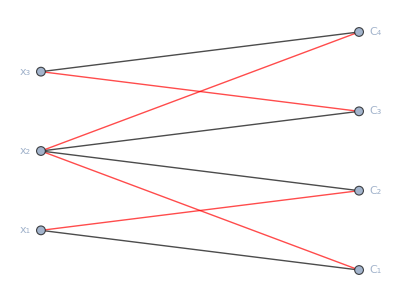

NCAlgebra::SmallCapSymbolsNonCommutative: All lower cap single letter symbols (e.g. a,b,c,...) were set as noncommutative.

Set::write: Tag Inherited in Inherited[State] is Protected.

Export::noopen: Cannot open C:\Users\He Entong\Downloads\IncGraph.pdf.

Set::write: Tag Inherited in Inherited[State] is Protected.

Export::noopen: Cannot open C:\Users\He Entong\Downloads\IncGraph.pdf.

Set::write: Tag Inherited in Inherited[State] is Protected.

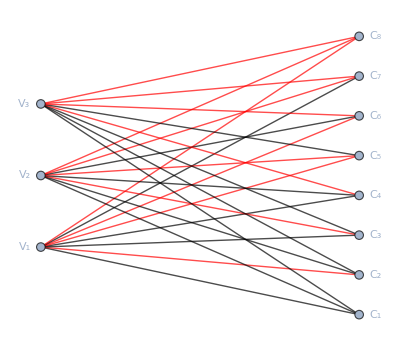

Set::write: Tag Inherited in Inherited[State] is Protected.

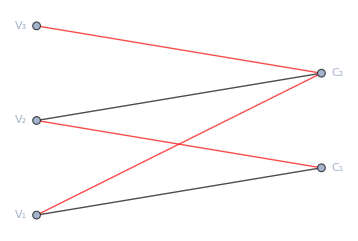

```mathematica
<< NCAlgebra`
<< NCGBX`

(* Form of an SAT instance: CNF = {Clause1, ..., Clause n}
Each clause element is specified by: {variable index, positivity (0 for positive, 1 for negative)}
 *)

CNFIncidenceGraph[CNF_] := Module[{vertices, edges = {}, numClauses, clauseVertices, varIndices = {}, variableVertices, edgeStyle = {}, graph},
vertices = {};
numClauses = Length[CNF];
For[i = 1, i <= numClauses, i++,
For[j = 1, j <= Length[CNF[[i]]], j++,
AppendTo[varIndices, CNF[[i,j,1]]];
];
];
varIndices = Union[varIndices];
clauseVertices = Table[Subscript[C, i], {i, 1, numClauses}];
variableVertices = Table[Subscript[x, i], {i, varIndices}];
For[i = 1, i <= Length[varIndices], i++,
AppendTo[vertices, variableVertices[[varIndices[[i]]]]];
];

For[i = 1, i <= numClauses, i++,
AppendTo[vertices, clauseVertices[[i]]];
For[j = 1, j <= Length[CNF[[i]]], j++,
AppendTo[edges, clauseVertices[[i]] <-> variableVertices[[CNF[[i, j, 1]]]]];
If[CNF[[i, j, 2]] == 0,
AppendTo[edgeStyle, clauseVertices[[i]] <-> variableVertices[[CNF[[i, j, 1]]]] -> Black],
AppendTo[edgeStyle, clauseVertices[[i]] <-> variableVertices[[CNF[[i, j, 1]]]] -> Red];
];
];
];

graph = Graph[vertices, edges, EdgeStyle->edgeStyle, VertexLabels->"Name", GraphLayout->"BipartiteEmbedding"];

Print[graph];
];

CNF={{{1,0},{2,0},{3,0}},(*Clause 1:x||y||z*){{1,1},{2,0},{3,0}},(*Clause 2:!x||y||z*){{1,0},{2,1},{3,0}},(*Clause 3:x||!y||z*){{1,0},{2,0},{3,1}},(*Clause 4:x||y||!z*){{1,1},{2,1},{4,0}},(*Clause 5:!x||!y||z*){{2,1},{3,0},{4,1}},(*Clause 6:!x||y||!z*){{1,0},{2,1},{3,1}},(*Clause 7:x||!y||!z*){{1,1},{4,1},{3,1}}   (*Clause 8:!x||!y||!z*)};

CNF={{{1,0},{2,1}},(*Clause 1:x1||!x2*){{1,1},{2,0}},(*Clause 2:!x1||x2*){{2,0},{3,1}},(*Clause 3:x2||!x3*){{2,1},{3,0}}   (*Clause 4:!x2||x3*)};

CNFIncidenceGraph[CNF];
```

```mathematica
vars={x, y, z};


clauses = {x || y || z, 
!x || y || z,
 x || !y || z,
 x || y || !z, 
!x || !y || z, 
!x || y || !z, 
x || !y || !z};

cnf=And@@clauses;


SatisfiableQ[cnf]
```

True